```mathematica
Subscript[y, i]==ⅇ^Subscript[z, i]/(∑_(j=1)^n ⅇ^Subscript[z, j])
(∂Subscript[y, i])/(∂Subscript[z, j])==Piecewise[{{Subscript[y, i] (1-Subscript[y, i]), i==j}, {-Subscript[y, i] Subscript[y, j], i≠j}}]
C==-∑_(j=1)^n Subscript[t, j] log(Subscript[y, j])
(∂C)/(∂Subscript[y, i])==-Subscript[t, i]/Subscript[y, i]
(∂C)/(∂Subscript[z, i])==∑_(j=1)^n (∂C)/(∂Subscript[z, j]) (∂Subscript[y, j])/(∂Subscript[z, i])==Subscript[y, i]-Subscript[t, i]
```

```mathematica
Clear[z]
n=3
Subscript[y, i_]:=ⅇ^Subscript[z, i]/∑_(j=1)^n ⅇ^Subscript[z, j]

D[Subscript[y, 1],Subscript[z, 1]]
D[Subscript[y, 1],Subscript[z, 2]]

Simplify[D[Subscript[y, 1],Subscript[z, 1]]==Subscript[y, 1](1-Subscript[y, 1])]
Simplify[D[Subscript[y, 1],Subscript[z, 2]]==-Subscript[y, 1] Subscript[y, 2]]

Subscript[y, i_]=.
cost=-∑_(j=1)^n Subscript[t, j] Log[Subscript[y, j]]
D[cost,Subscript[y, 1]]
D[cost,Subscript[y, 2]]
```

3

-ⅇ^(2 z_1)/((ⅇ^z_1+ⅇ^z_2+ⅇ^z_3)^2)+ⅇ^z_1/(ⅇ^z_1+ⅇ^z_2+ⅇ^z_3)

-ⅇ^(z_1+z_2)/((ⅇ^z_1+ⅇ^z_2+ⅇ^z_3)^2)

True

True

-Log[y_1] t_1-Log[y_2] t_2-Log[y_3] t_3

-t_1/y_1

-t_2/y_2

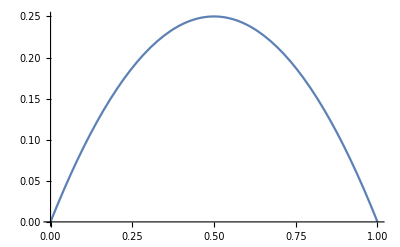

```mathematica
Plot[y(1 - y), {y, 0, 1}]
```

```mathematica
Plot3D[{ⅇ^Subscript[z, 1]/(ⅇ^Subscript[z, 1]+ⅇ^Subscript[z, 2]),ⅇ^Subscript[z, 2]/(ⅇ^Subscript[z, 1]+ⅇ^Subscript[z, 2])},{Subscript[z, 1],-5,5},{Subscript[z, 2],-5,5}]
```

-Graphics3D-

True

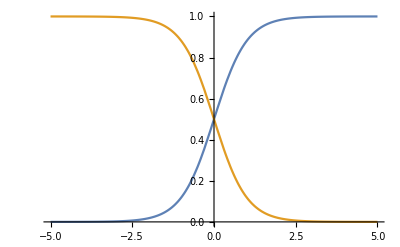

```mathematica
σ[z_]:=1/(1+ⅇ^-z)
Simplify[σ[2z]==ⅇ^Subscript[z, 1]/(ⅇ^Subscript[z, 1]+ⅇ^Subscript[z, 2])/.{Subscript[z, 1]->z,Subscript[z, 2]->-z}]
Plot[{σ[2z],σ[-2z]},{z,-5,5}]
```

-1/y

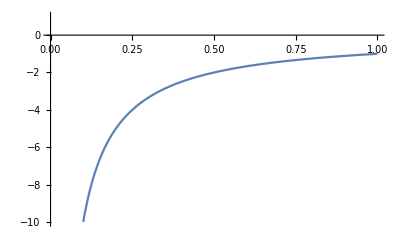

```mathematica
Dt[-Log[y],y]
Plot[%,{y,0,1},PlotRange->{-10,1}]
```

```mathematica
n=3
Subscript[y, i_]:=ⅇ^Subscript[z, i]/∑_(j=1)^n ⅇ^Subscript[z, j]
{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3]}/.{Subscript[z, 1]->x+y,Subscript[z, 2]->x-y,Subscript[z, 3]->y-x}
Plot3D[%,{x,-3,3},{y,-3,3}]
```

3

{ⅇ^(x+y)/(ⅇ^(x-y)+ⅇ^(-x+y)+ⅇ^(x+y)),ⅇ^(x-y)/(ⅇ^(x-y)+ⅇ^(-x+y)+ⅇ^(x+y)),ⅇ^(-x+y)/(ⅇ^(x-y)+ⅇ^(-x+y)+ⅇ^(x+y))}

-Graphics3D-

```mathematica
s[z_]:=Exp[z]/Total[Exp[z]]
Simplify[s[{x+c,y+c,z+c}]== s[{x,y,z}]]
```

True